## sampleBall

```mathematica
sampleBall[d_:2]:=Normalize[RandomVariate[MultinormalDistribution[ConstantArray[0,d],IdentityMatrix[d]]]]*Power[RandomReal[],1/d];
```

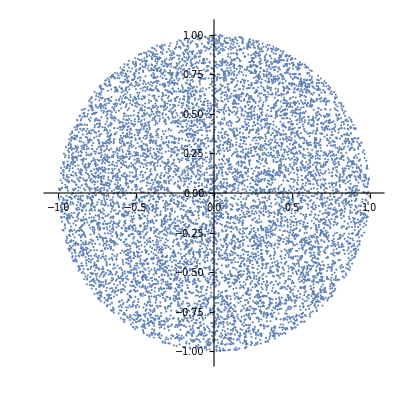

```mathematica
ListPlot[Table[sampleBall[],{i,10000}],PlotRange->1.05{{-1,1},{-1,1}},AspectRatio->1]
```

```mathematica
ListPointPlot3D[Table[sampleBall[3],{i,10000}],BoxRatios->ConstantArray[3,1],PlotRange->{{-1,1},{-1,1},{-1,1}}]
```

-Graphics3D-

One of these points is special

## guesses

```mathematica
ClearAll[xGT]
xGT[d_:3]:=sampleBall[d]
```

```mathematica
ClearAll[oracle];
oracle[xGT_][xA_,xB_]:=If[EuclideanDistance[xA,xGT]≤EuclideanDistance[xB,xGT],xA,xB]
```

```mathematica
ClearAll[oracularOrderingFunction];
oracularOrderingFunction[xGT_][xA_,xB_]:=EuclideanDistance[xA,xGT]≤EuclideanDistance[xB,xGT]
```

```mathematica
ClearAll[guesses];
guesses[xGT_][d_:3,n_:20]:=Sort[Table[sampleBall[d],{i,n}],oracularOrderingFunction[xGT]];
```

Five iterations of the 1D experiment. Notice the bends. What do they mean? How did they get there?

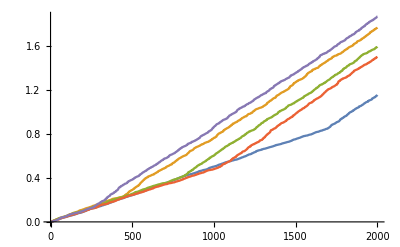

```mathematica
ListLinePlot[
Table[
With[{d=1,n=2000},
With[{xgt=xGT[d]},
EuclideanDistance[#,xgt]&/@guesses[xgt][d,n]]],{m,5}]]
```

Verify that “guesses” is working.

```mathematica
xgt1$=xGT[1]
xp1$=guesses[xgt1$][1,10]
```

{0.554763}

{{0.47961},{0.462353},{0.728577},{0.813735},{0.855869},{0.22758},{0.136459},{-0.773355},{-0.944688},{-0.945502}}

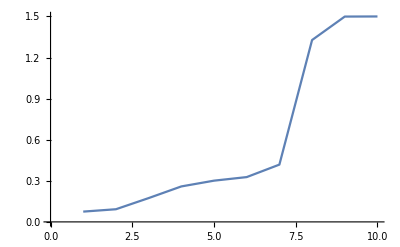

```mathematica
ListLinePlot[EuclideanDistance[#,xgt1$]&/@xp1$]
```

## firstDifference

```mathematica
ClearAll[firstDifference];
firstDifference[list_]:=#[[2]]-#[[1]]&/@Partition[list,2,1];
```

## checkMonotonicity

```mathematica
ClearAll[checkMonotonicity];
checkMonotonicity[d_,n_]:=
With[{xgt=xGT[d]},
With[{xp=guesses[xgt][d,n]},
With[{ds=EuclideanDistance[#,xgt]&/@xp},
With[{diffs=firstDifference[ds]},
Select[diffs,#<0&]]]]];
```

```mathematica
checkMonotonicity[12,1000]
```

{}

{-0.627969}

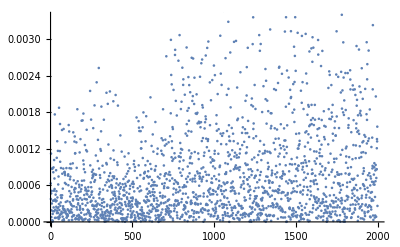
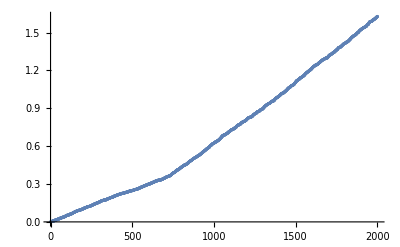
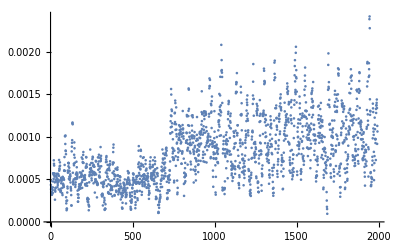
-Graphics- | -Graphics-
-Graphics- |

```mathematica
xgt1$=xGT[1]
xp1$=guesses[xgt1$][1,2000];
Grid[{{ListPlot[firstDifference[EuclideanDistance[#,xgt1$]&/@xp1$]],
ListPlot[EuclideanDistance[#,xgt1$]&/@xp1$]},
{ListPlot[MovingAverage[firstDifference[EuclideanDistance[#,xgt1$]&/@xp1$],7]]}}]
```

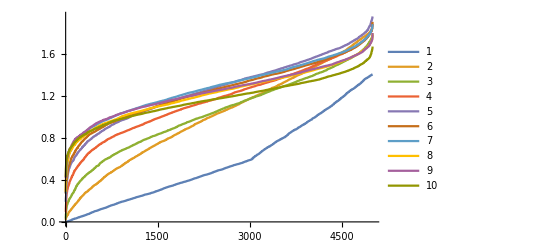

```mathematica
ListLinePlot[
With[{n=5000},
Table[
With[{xgt=xGT[d]},
EuclideanDistance[#,xgt]&/@guesses[xgt][d,n]],{d,1,10}]],
PlotLegends->Automatic]
```

```mathematica
xGT1=xGT[1]
```

{0.635984}

```mathematica
experiment1$=guesses[xGT1][1,2000];
```

Take each guess in turn, pretend it’s xGT, calculate the mean Euclidean distance of the entire sorted list.

```mathematica
distances$=Table[
Mean[EuclideanDistance[#,turn]&/@experiment1$],
{turn,experiment1$}];
```

```mathematica
xGT1
```

{0.635984}

```mathematica
ClearAll[experiment];
experiment[xgt_][d_,n_]:=
With[{gs=guesses[xgt][d,n]},
With[{ds=Table[Mean[EuclideanDistance[#,turn]&/@gs],{turn,gs}]},
Print[MatrixForm[gs]];
Print[MatrixForm[ds]];
ListPlot[ds]]];
```

(0.535266
0.808464
0.853657
0.153941
0.111826
0.0935781
-0.17764
-0.200338
-0.239186
-0.252368
-0.267364
-0.308811
-0.324029
-0.342888
-0.433513
-0.563903
-0.588902
-0.705195
-0.8406
-0.902042)

(0.773927
0.992485
1.03316
0.507
0.481731
0.472607
0.364119
0.35731
0.349541
0.348222
0.348222
0.352367
0.355411
0.361068
0.397319
0.462513
0.477513
0.558918
0.667242
0.72254)

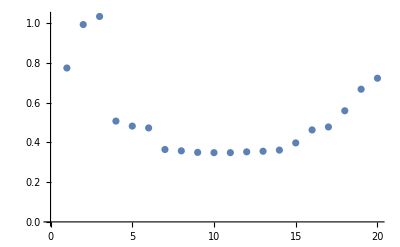

```mathematica
experiment[xGT1][1,20]
```

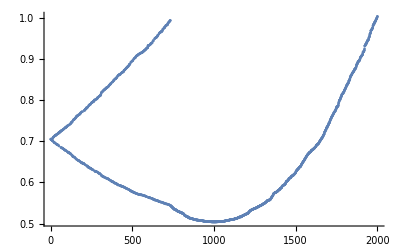

```mathematica
ListPlot[distances$]
```